```mathematica
ShowGraphsFor2[nodes_]:=Map[First,Tally[Flatten[Monitor[
Table[With[
{g=GraphUnion[
GraphComplement[Graph[GraphFromSets[s1]]],
GraphComplement[Graph[GraphFromSets[s2]]],
GraphComplement[Graph[GraphFromSets[s3]]],
GraphComplement[Graph[GraphFromSets[s4]]],
GraphComplement[Graph[GraphFromSets[s5]]]
]},
Graph[g, VertexLabels->"Name"]
],{s1,quad1[nodes]},{s2,quad2[nodes]},{s3,quad3[nodes]},{s4,quad4[nodes]},{s5,quad5[nodes]}],
{s1,s2,s3,s4,s5}
]],IsomorphicGraphQ]
]
```

```mathematica
ShowGraphsFor3[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,e3,e4,e5,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
e3=EdgeList[GraphComplement[Graph[GraphFromSets[s3]]]];
e4=EdgeList[GraphComplement[Graph[GraphFromSets[s4]]]];
e5=EdgeList[GraphComplement[Graph[GraphFromSets[s5]]]];
all=DeleteDuplicates[Join[e1,e2,e3,e4,e5]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]},{s3,Take[quad3[nodes],take]},{s4,Take[quad4[nodes],take]},{s5,Take[quad5[nodes],take]}],
{s1,s2,s3,s4,s5}
],5]
```

```mathematica
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3[6,4]]
```

{16,20,16,20,15,20,15,20,12,20,12,16,16,25,16,16,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,16,20,16,20,15,20,15,20,12,20,12,16,16,25,16,16,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,20,20,20,25,15,20,15,20,15,20,15,20,20,25,20,20,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,20,20,20,25,15,20,15,20,15,20,15,20,20,25,20,20,20,20,20,25,20,20,20,25,20,20,20,25,25,25,25,25,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,20,25,20,20,25,25,25,25,20,25,20,20,20,25,20,20,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,16,16,20,20,11,16,15,15,15,20,15,20,15,20,20,15,20,20,25,20,15,20,20,15,20,25,20,20,15,20,20,15,20,20,20,25,15,20,15,20,15,20,15,20,20,25,20,20,16,16,20,20,16,16,20,20,20,20,20,25,20,20,25,20,16,16,20,20,11,16,15,15,15,20,15,20,15,20,20,15,20,20,25,20,15,16,16,12,20,20,16,16,15,16,16,12,20,20,20,25,15,15,11,16,15,15,11,16,20,20,16,16,16,16,20,20,16,12,15,16,20,15,15,20,20,16,20,16,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,25,25,25,25,25,20,20,20,25,20,20,20,25,20,20,20,16,16,20,20,16,16,20,20,20,20,20,25,20,20,25,20,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,20,20,25,20,15,15,20,20,15,15,20,25,20,20,20,16,16,20,20,16,12,15,16,20,15,15,20,20,16,20,16,12,16,16,15,16,16,20,20,16,20,16,20,15,20,20,15,20,20,25,20,20,20,25,20,25,25,25,25,20,20,25,20,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,12,16,16,15,16,16,20,20,16,20,16,20,15,20,20,15,16,16,20,20,16,16,20,20,20,20,20,25,20,20,25,20,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,20,20,25,20,15,15,20,20,15,15,20,25,20,20,20,16,16,20,20,16,12,15,16,20,15,15,20,20,16,20,16,20,25,20,20,25,25,25,25,20,25,20,20,20,25,20,20,25,25,25,25,25,20,20,20,25,20,20,20,25,20,20,20,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,12,16,16,15,16,16,20,20,16,20,16,20,15,20,20,15,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,16,20,16,20,20,15,15,20,16,15,11,15,20,20,15,15,12,16,16,15,16,12,15,16,16,15,11,15,15,16,15,11,15,20,20,15,15,20,20,15,16,25,16,16,11,20,16,11,20,20,25,20,15,20,20,15,20,25,20,20,15,20,20,15,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,15,20,20,15,20,20,25,20,20,25,20,20,15,20,20,15,20,20,25,20,15,20,20,15,20,25,20,20,15,20,20,15,20,20,25,20,15,16,16,12,20,20,16,16,15,16,16,12,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,20,25,20,20,20,20,16,16,16,20,12,12,16,20,12,12,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,15,20,20,15,20,20,25,20,20,25,20,20,15,20,20,15,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,15,20,20,15,20,16,20,16,20,20,15,15,15,16,15,11}

```mathematica
ShowGraphsFor3Four[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,e3,e4,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
e3=EdgeList[GraphComplement[Graph[GraphFromSets[s3]]]];
e4=EdgeList[GraphComplement[Graph[GraphFromSets[s4]]]];
all=DeleteDuplicates[Join[e1,e2,e3,e4]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]},{s3,Take[quad3[nodes],take]},{s4,Take[quad4[nodes],take]}],
{s1,s2,s3,s4}
],4]
```

```mathematica
quad2[6]//Length
```

4

```mathematica
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3Four[6,4]]//Tally//Sort
```

{{7,1},{8,12},{9,12},{11,57},{12,60},{15,96},{19,18}}

```mathematica
ShowGraphsFor3Three[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,e3,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
e3=EdgeList[GraphComplement[Graph[GraphFromSets[s3]]]];
all=DeleteDuplicates[Join[e1,e2,e3]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]},{s3,Take[quad3[nodes],take]}],
{s1,s2,s3}
],3]
```

```mathematica
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3Three[6,4]]//Tally//Sort
```

{{4,4},{5,8},{6,6},{7,22},{8,13},{10,10},{13,1}}

```mathematica
ShowGraphsFor3Two[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
all=DeleteDuplicates[Join[e1,e2]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]}],
{s1,s2}
],2]
```

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3Two[nodes,count]]//Tally//Sort
],
{nodes,5,9}
],
nodes],
TableDepth->1
]
```

{{2,1}}
{{2,5},{3,4},{4,7}}
{{2,31},{3,56},{4,74},{5,24},{6,36},{8,35}}
{{2,311},{3,672},{4,774},{5,480},{6,600},{7,132},{8,480},{9,88},{10,240},{12,168},{16,151}}
{{2,5059},{3,9560},{4,8402},{5,7056},{6,8304},{7,3072},{8,5040},{9,2928},{10,4440},{11,680},{12,3528},{13,240},{14,900},{15,240},{16,2556},{17,160},{18,840},{20,1320},{24,600},{32,611}}

```mathematica
PrintLength[s_,more_:""]:=Block[{},Print["Length is ",Length[s], " ", more];s]
```

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Two[nodes,count],"all graphs"],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,5,10}
],
nodes],
TableDepth->1
]
```

Length is 1 all graphs

Length is 1 isomorphic

Length is 16 all graphs

Length is 7 isomorphic

Length is 256 all graphs

Length is 29 isomorphic

Length is 4096 all graphs

Length is 109 isomorphic

{{2,1}}
{{2,3},{3,1},{4,3}}
{{2,8},{3,4},{4,8},{5,2},{6,2},{8,5}}
{{2,18},{3,12},{4,22},{5,11},{6,10},{7,3},{8,14},{9,3},{10,4},{12,3},{16,9}}

```mathematica
4096*16*16
```

1048576

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Three[nodes,count],"all graphs"],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,5,8}
],
nodes],
TableDepth->1
]
```

Length is 1 all graphs

Length is 1 isomorphic

Length is 64 all graphs

Length is 17 isomorphic

Length is 4096 all graphs

Length is 226 isomorphic

Length is 262144 all graphs

Length is 3233 isomorphic

{{3,1}}
{{4,3},{5,3},{6,1},{7,4},{8,2},{10,3},{13,1}}
{{3,1},{4,8},{5,4},{6,11},{7,9},{8,18},{9,11},{10,11},{11,14},{12,14},{13,10},{14,6},{15,16},{16,10},{17,8},{18,10},{19,4},{20,4},{21,5},{22,16},{24,2},{25,8},{26,6},{29,4},{32,10},{33,1},{34,1},{42,3},{55,1}}
{{3,7},{4,31},{5,27},{6,56},{7,41},{8,95},{9,54},{10,100},{11,54},{12,129},{13,72},{14,82},{15,79},{16,113},{17,79},{18,100},{19,85},{20,95},{21,83},{22,55},{23,82},{24,96},{25,79},{26,55},{27,64},{28,70},{29,43},{30,79},{31,90},{32,30},{33,29},{34,81},{35,49},{36,35},{37,44},{38,66},{39,20},{40,51},{41,27},{42,25},{43,31},{44,28},{45,38},{46,80},{47,12},{48,14},{49,8},{50,46},{51,5},{52,29},{53,24},{54,10},{55,3},{56,56},{57,9},{58,11},{59,14},{60,6},{61,15},{62,14},{63,8},{64,5},{65,1},{66,20},{67,4},{68,48},{69,5},{70,7},{71,2},{74,11},{75,3},{77,15},{78,15},{81,1},{82,23},{83,1},{87,3},{88,1},{90,6},{92,1},{99,1},{100,24},{103,2},{108,4},{119,4},{132,7},{135,1},{142,1},{174,3},{229,1}}

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Four[nodes,count],"all graphs"],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,5,7}
],
nodes],
TableDepth->1
]
```

Length is 1 all graphs

Length is 1 isomorphic

Length is 256 all graphs

Length is 16 isomorphic

Length is 65536 all graphs

Length is 240 isomorphic

{{4,1}}
{{7,1},{8,3},{9,2},{11,4},{12,2},{15,3},{19,1}}
{{7,4},{8,6},{9,4},{10,4},{11,5},{12,7},{13,8},{14,14},{15,4},{16,8},{17,9},{18,15},{19,3},{20,8},{21,11},{22,3},{23,2},{24,2},{25,18},{26,12},{27,2},{28,9},{29,9},{30,5},{31,2},{32,2},{33,3},{34,3},{36,18},{38,1},{39,3},{40,8},{41,5},{47,4},{51,12},{52,1},{53,1},{66,4},{85,1}}

```mathematica
262144*64
```

16777216

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,Tally[ShowGraphsFor3Three[nodes,count],IsomorphicGraphQ]]]//Tally//Sort
],
{nodes,5,8}
],
nodes],
TableDepth->1
]
```

$Aborted

```mathematica
Map[Map[HasQuadrilateralPattern,Map[SymbolToSets,Select[FindFullFormula[#],SymbolLevel[#]==4&]]]&,ShowGraphsFor3[6,2]]
```

{{True,True,True,True,True,True,False,True,True,False,True,False,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,False,False,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False,True,False,True,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False,True,False,True,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,True,True,True,True,False,False,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False,True,False,True,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,False,False,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False,True,False,True,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False,True,False,True,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,True,True,True,True,False,False,True,True,True,False,False},{True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False,True,False,True,True,True,True,False,False},{True,True,True,True,True,True,False,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,False,True,False,True,True,True,False,False},{True,True,True,False,True,False,False,True,True,False,False},{True,True,True,True,True,True,False,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,True,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,True,True,True,False,True,False,True,True,True,False,False},{True,True,True,False,True,True,True,True,True,False,False,True,True,False,False},{True,True,True,True,True,True,False,True,True,True,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,False,True,False,True,True,True,False,False},{True,True,True,False,True,False,False,True,True,False,False},{True,True,True,True,True,True,False,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,True,True,True,False,True,False,True,True,True,False,False},{True,True,True,True,True,True,False,True,True,True,True,True,False,True,False,True,True,True,False,False},{True,True,True,False,True,True,True,True,True,False,False,True,True,False,False},{True,True,True,True,False,True,True,True,True,False,True,False,True,True,False,False}}

```mathematica
Table[Map[PlanarGraphQ,ShowGraphsFor3[k,2]],{k,6,10}]
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,False,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,False,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,False,True,True,True,True,True}}

```mathematica
Map[HasTrianglePattern,Map[SymbolToSets,FindFullFormula[First[ShowGraphsFor3[8]]]]]//Tally
```

{{False,302},{True,119}}

General::stop: Further output of 
StyleBox[
 RowBox[{\"Part\", \"::\", \"partd\"}], \"MessageName\"] will be suppressed during this calculation.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

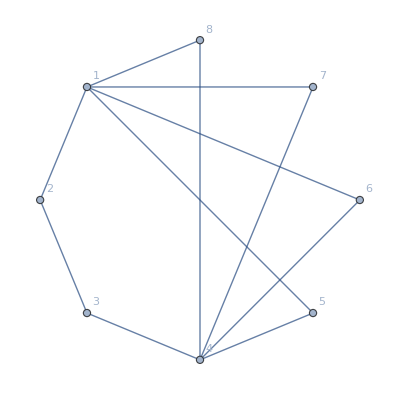
```mathematica
Map[SymbolLevel,FindFullFormula[-Graphics-]]//Tally//Sort
```

{{3,19},{4,118},{5,176},{6,90},{7,17},{8,1}}

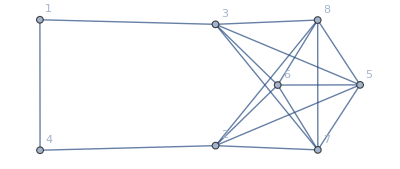
```mathematica
ChromaticPolynomial[-Graphics-,x]//Factor
```

(-4+x) (-3+x) (-2+x) (-1+x) x (-13+15 x-7 x^2+x^3)

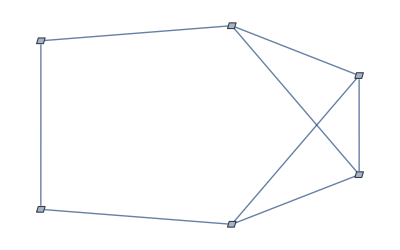
```mathematica
{Graph[EdgeDelete[-Graphics-,1<->2],VertexLabels->"Name"]}
```

```mathematica
gr=ShowGraphsFor2[6];
```

```mathematica
Length[gr]
```

6

```mathematica
grSets=Map[Map[SymbolToSets,FindFullFormula[#]]&,gr];
```

```mathematica
HasTrianglePattern[s_]:=PartitionHasPatternFast[s,{{1,3},{2,4},{5}}]||
PartitionHasPatternFast[s,{{1,4},{2},{3,5}}]||
PartitionHasPatternFast[s,{{1},{2,4},{3,5}}]||
PartitionHasPatternFast[s,{{1,4},{2,5},{3}}]||
PartitionHasPatternFast[s,{{1,3},{2,5},{4}}]
```

```mathematica
HasQuadrilateralPattern[s_]:=PartitionHasPatternFast[s,{{1},{2},{3,5},{4}}]||
PartitionHasPatternFast[s,{{1,3},{2},{4},{5}}]||
PartitionHasPatternFast[s,{{1,4},{2},{3},{5}}]||
PartitionHasPatternFast[s,{{1},{2,5},{3},{4}}]||
PartitionHasPatternFast[s,{{1},{2,4},{3},{5}}]
```

```mathematica
f=Select[First[grSets],Length[#]==4&]
```

{{{1},{2,3},{4,6},{5}},{{1},{2,3},{4,5},{6}},{{1,6},{2},{3},{4,5}},{{1,6},{2},{3,4},{5}},{{1,6},{2,3},{4},{5}},{{1,5},{2},{3},{4,6}},{{1,5},{2},{3,4},{6}},{{1,5},{2,3},{4},{6}},{{1,2},{3},{4,6},{5}},{{1,2},{3},{4,5},{6}},{{1,2},{3,4},{5},{6}}}

```mathematica
Map[HasQuadrilateralPattern,quad1[6]]
```

{True,True,True,True}

```mathematica
Map[HasQuadrilateralPattern,Select[First[grSets],Length[#]==4&]]
```

{False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Map[Map[HasTrianglePattern,#]&,grSets]
```

{{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}}